```mathematica
()
```

```mathematica
Subscript[a, n]=(8 n^4+3n-8)/(2 n^4+8n+5)
{Limit[Subscript[a, n],n->∞],Limit[(Subscript[a, n]/.n->n+1)/Subscript[a, n],n->∞],Limit[Subscript[a, n]^(1/n),n->∞],∫_1^∞ Subscript[a, n] ⅆn}
```

(-8+3 n+8 n^4)/(5+8 n+2 n^4)

Integrate::idiv: Integral of -8 + 3\ n + 8\ n^4/5 + 8\ n + 2\ n^4 does not converge on {1, ∞}.

{4,1,1,∫_1^∞ (-8+3 n+8 n^4)/(5+8 n+2 n^4)ⅆn}

```mathematica
Subscript[a, n]=(8 n^3+5)/9^(8n+1)
{Limit[Subscript[a, n],n->∞],Limit[(Subscript[a, n]/.n->n+1)/Subscript[a, n],n->∞],Limit[Subscript[a, n]^(1/n),n->∞],∫_1^∞ Subscript[a, n] ⅆn}
```

9^(-1-8 n) (5+8 n^3)

{0,1/43046721,1/43046721,(3+24 Log[9]+96 Log[9]^2+416 Log[9]^3)/(99179645184 Log[9]^4)}

```mathematica
Subscript[a, n]=((n^3+8n-2)/(n^3-8n+7))^(8n+1)
{Limit[Subscript[a, n],n->∞],Limit[(Subscript[a, n]/.n->n+1)/Subscript[a, n],n->∞],Limit[Subscript[a, n]^(1/n),n->∞],∫_1^∞ Subscript[a, n] ⅆn}
```

((-2+8 n+n^3)/(7-8 n+n^3))^(1+8 n)

Integrate::idiv: Integral of (1/7 - 8\ n + n^3)^1 + 8\ n\ (-2 + 8\ n + n^3)^1 + 8\ n does not converge on {1, ∞}.

{1,1,1,∫_1^∞ ((-2+8 n+n^3)/(7-8 n+n^3))^(1+8 n)ⅆn}

```mathematica
∫(8x+1)Cosh[8x]ⅆx
```

-1/8 Cosh[8 x]+1/8 Sinh[8 x]+x Sinh[8 x]

```mathematica
∫ⅇ^(8x)Sin[x]ⅆx
```

-1/65 ⅇ^(8 x) (Cos[x]-8 Sin[x])

```mathematica
∫_-1^8 (8x-x^8+8)ⅆx
```

-14912757

```mathematica
Limit[(x^2-9x+8)/(x^2-1),x->1]
```

-7/2

```mathematica
Limit[Tan[8x]/(ⅇ^(8x)-1),x->0]
```

1

```mathematica
Limit[((x+1)/(x-8))^(8x+1),x->∞]
```

ⅇ^72

```mathematica
z=x^8 y+Sinh[8x]-Tan[8xy]
```

x^8 y+Sinh[8 x]-Tan[8 xy]

```mathematica
D[z,{x,2}]
```

56 x^6 y+64 Sinh[8 x]

```mathematica
D[z,{x,1},{y,1}]
```

8 x^7

```mathematica
D[z,{y,1},{x,1}]
```

8 x^7

```mathematica
D[z,{y,2}]
```

0

```mathematica
z=(8x-y^8)/Log[2,(8x+y)]
```

((8 x-y^8) Log[2])/Log[8 x+y]

```mathematica
D[z,{x,2}]
```

(8 x-y^8) Log[2] (128/((8 x+y)^2 Log[8 x+y]^3)+64/((8 x+y)^2 Log[8 x+y]^2))-(128 Log[2])/((8 x+y) Log[8 x+y]^2)

```mathematica
D[z,{x,1},{y,1}]
```

(16 (8 x-y^8) Log[2])/((8 x+y)^2 Log[8 x+y]^3)-(8 Log[2])/((8 x+y) Log[8 x+y]^2)+(64 y^7 Log[2])/((8 x+y) Log[8 x+y]^2)+(8 (8 x-y^8) Log[2])/((8 x+y)^2 Log[8 x+y]^2)

```mathematica
D[z,{y,1},{x,1}]
```

(16 (8 x-y^8) Log[2])/((8 x+y)^2 Log[8 x+y]^3)-(8 Log[2])/((8 x+y) Log[8 x+y]^2)+(64 y^7 Log[2])/((8 x+y) Log[8 x+y]^2)+(8 (8 x-y^8) Log[2])/((8 x+y)^2 Log[8 x+y]^2)

```mathematica
D[z,{y,2}]
```

(8 x-y^8) Log[2] (2/((8 x+y)^2 Log[8 x+y]^3)+1/((8 x+y)^2 Log[8 x+y]^2))+(16 y^7 Log[2])/((8 x+y) Log[8 x+y]^2)-(56 y^6 Log[2])/Log[8 x+y]

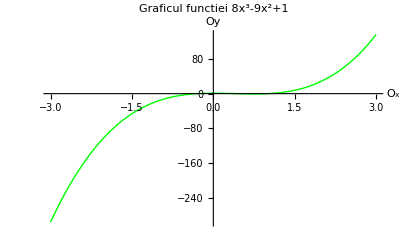

```mathematica
Plot[{8 x^3-9 x^2+1},{x,-3,3},AxesLabel->{"O_x","Oy"},PlotStyle->Green,PlotLabel->"Graficul functiei 8x^3-9x^2+1"]
```

Graphics::gprim: Reed was encountered where a Graphics primitive or directive was expected.

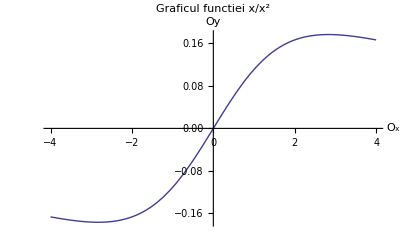

```mathematica
Plot[{x/(x^2+8)},{x,-4,4},AxesLabel->{"O_x","Oy"},PlotStyle->Reed,PlotLabel->"Graficul functiei x/x^2"]
```

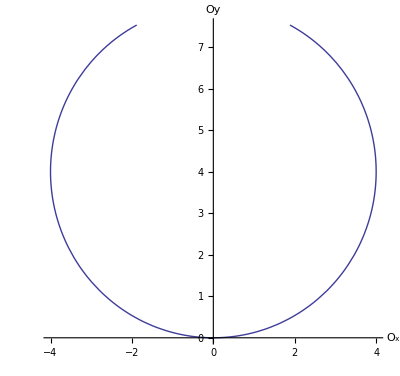

```mathematica
ParametricPlot[{(8t)/(1+t^2),(8 t^2)/(1+t^2)},{t,-4,4},AxesLabel->{"O_x","Oy"}]
```

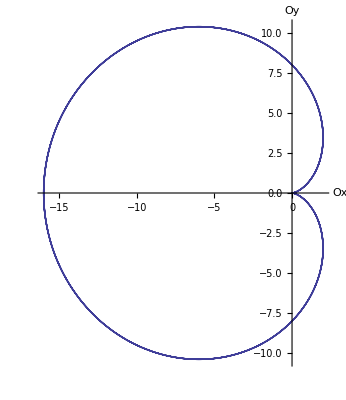

```mathematica
PolarPlot[8(1-Cos[φ]),{φ,-4π,4π},AxesLabel->{"Ox","Oy"}]
```

```mathematica
y=x^2(x-8)
(*DVA*)
Solve[Denominator[y]==0,x]
```

(-8+x) x^2

{}

```mathematica
(*Stabilim punctele critice y'=0*)
Solve[D[y,x]==0,x]
```

{{x→0},{x→16/3}}

```mathematica
(*Determinam semnul derivatei pe intervalele*)
D[y,x]/.x->{-1,5,8}
```

{19,-5,64}

```mathematica
{Subscript[y, min]=y/.x->0,Subscript[y, max]=y/.x->16/3}
```

{0,-2048/27}

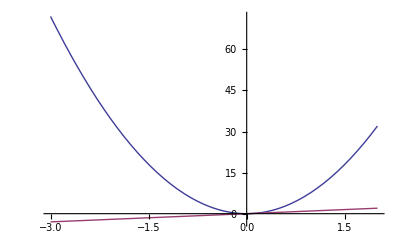

```mathematica
(*Construim domeniul*)
Plot[{8 x^2,x},{x,-3,2}]
```

```mathematica
Solve[{y==8 x^2,y==x},{x,y}]
```

```mathematica
{{y->0,x->0},{y->1/8,x->1/8}}
S=∫_(1/8)^(1/8) (x-8 x^2)ⅆx
```

{{y→0,x→0},{y→1/8,x→1/8}}

0

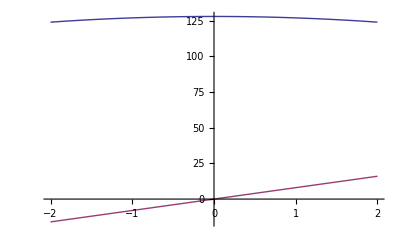

```mathematica
Plot[{128-x^2,8x},{x,-2,2}]
```

```mathematica
Solve[{y==128-x^2,y==8x},{x,y}]
```

{{y→-128,x→-16},{y→64,x→8}}

```mathematica
S=∫_8^64 (x-128-x^2)ⅆx
```

-277088/3

```mathematica
Series[Sin[8x],{x,0,7}]
```

8 x-(256 x^3)/3+(4096 x^5)/15-(131072 x^7)/315+O[x]^8

```mathematica
Series[ⅇ^(x/8),{x,0,5}]
```

1+x/8+x^2/128+x^3/3072+x^4/98304+x^5/3932160+O[x]^6

```mathematica
ContourPlot3D[{x+8y+z==8,x==0,y==0,z==0},{x,0,8},{y,0,8},{z,0,8}]
```

-Graphics3D-

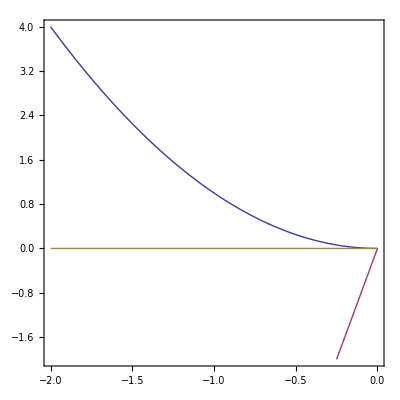

```mathematica
ContourPlot[{y==x^2,y==8x,y==0},{x,-2,0},{y,-2,4}]
```